# Doubly Periodic with Lines

(2 - Parameter Version)

## Weierstrass Data

Two parameters:

0 < α < π/2, 0 <= ϕ <= α

```mathematica
α=Pi/2-Pi/8//N;
ϕ=Pi/4//N;
ϵ=E^(I ϕ);
```

```mathematica
G[z_]:=(z+ϵ)/( z-ϵ);
dh[z_]:=I/( Sqrt[z^2-Cos[2 α]-√(-1+Cos[2 α]^2)]Sqrt[z^2-Cos[2 α]+√(-1+Cos[2 α]^2)])
```

```mathematica
phi1[z_]:=G[z]dh[z]; 
phi2[z_]:=1/G[z]dh[z]; 

ω1[z_] :=( phi2[z]-phi1[z])/2;
ω2[z_] :=I( phi1[z]+phi2 [z])/2;
ω3[z_] :=dh[z];
```

```mathematica
f1[w_] :=  Re[NIntegrate[{ω1[z],ω2[z],ω3[z]},{z,+0.1I,w}]]
```

## Parametrization

```mathematica
g[z_]:=E^(I ϕ)(-z+I)/(z+I)
```

```mathematica
f0=f1[g[N[Cot[(α+ϕ)/2]]]]
```

{0.595003,-0.638299,-1.09981}

```mathematica
f[w_] :=  Re[NIntegrate[{ω1[z],ω2[z],ω3[z]},{z,+0.1I,w}]]-f0
```

```mathematica
n[z_]:=StereographicProjection[G[z]]
```

Translational vectors:

```mathematica
{dummy,disy,disz}=(f[g[1]]+f[g[-1]])
```

{1.0284×10^-8,1.27794,2.40009}

```mathematica
disx=f[g[N[Tan[(α-ϕ)/2]]]][[1]]
```

-2.64175

```mathematica
xmin=0.01;
```

```mathematica
{xmin,N[Tan[(α-ϕ)/2]],N[Tan[(α+ϕ)/2]],1}
```

{0.01,0.198912,1.49661,1}

```mathematica
xspec0=Sort[{xmin,N[Tan[(α-ϕ)/2]],N[Tan[(α+ϕ)/2]],1}];
```

```mathematica
xspec=Union[xspec0,1/xspec0,SameTest->AlmostEqual];
```

```mathematica
xspec
```

{0.01,0.198912,0.668179,1,1.49661,5.02734,100.}

```mathematica
nx=5;
fff[{x_,y_}]:=ExpNRange[x,y,nx];
xr=Union[Flatten[fff/@Partition[xspec,2,1]],SameTest->AlmostEqual];
```

```mathematica
eps=.00000001;
```

```mathematica
domain1=PolarDomain[xr,NRange[eps,Pi-eps,11]];
```

```mathematica
domain2=MeshApply[g,domain1];
```

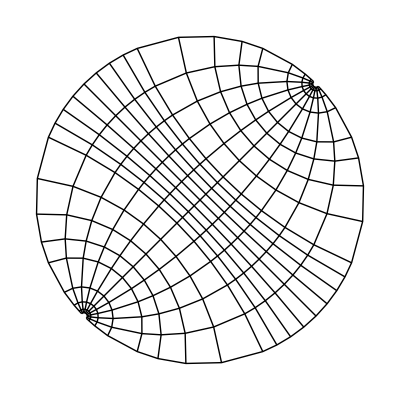

```mathematica
Show[DomainToGraphics[domain2]]
```

```mathematica
m1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain2];
```

```mathematica
m2=MeshJoin[m1,MeshReflect[m1,Plane[{1,0,0},0]]];
```

```mathematica
m3=MeshJoin[m2,MeshRotate[m2,StraightLine[{0,0,0},{1,0,0}]]];
```

```mathematica
m4=MeshJoin[m3,MeshTranslate[m3,2{0,disy,disz}]];
```

```mathematica
m5=MeshJoin[MeshTranslate[m4,{-disx,0,0}],MeshTranslate[m4,{disx,0,0}]];
```

```mathematica
Show[gr =Mesh3DToGraphicsComplex[m5,{FaceForm[Pink,LightBlue]}],Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
Show[Mesh3DToGraphics3D[m3],Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-

## Raytrace Translational Fundamental Piece

```mathematica
nx=20;
ny=20;

fff[{x_,y_}]:=ExpNRange[x,y,nx];
XR=Union[Flatten[fff/@Partition[xspec,2,1]],SameTest->AlmostEqual];
xr={xmin,1,1/xmin};
YR=NRange[0,Pi,ny];
yr=NRange[0,Pi,2];


domain1=PolarDomain[XR,YR];
domain2=MeshApply[g,domain1];
m1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain2];
m2=MeshJoin[m1,MeshReflect[m1,Plane[{1,0,0},0]]];
m3=MeshJoin[m2,MeshRotate[m2,StraightLine[{0,0,0},{1,0,0}]]];
mXY=m3;

domain1=PolarDomain[xr,yr];
domain2=MeshApply[g,domain1];
m1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain2];
m2=MeshJoin[m1,MeshReflect[m1,Plane[{1,0,0},0]]];
m3=MeshJoin[m2,MeshRotate[m2,StraightLine[{0,0,0},{1,0,0}]]];
mxy=m3;

domain1=PolarDomain[XR,yr];
domain2=MeshApply[g,domain1];
m1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain2];
m2=MeshJoin[m1,MeshReflect[m1,Plane[{1,0,0},0]]];
m3=MeshJoin[m2,MeshRotate[m2,StraightLine[{0,0,0},{1,0,0}]]];
mXy=m3;

domain1=PolarDomain[xr,YR];
domain2=MeshApply[g,domain1];
m1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain2];
m2=MeshJoin[m1,MeshReflect[m1,Plane[{1,0,0},0]]];
m3=MeshJoin[m2,MeshRotate[m2,StraightLine[{0,0,0},{1,0,0}]]];
mxY=m3;

PoVExport["dummy",mXY,mxy,mxY,mXy];
```

## Raytrace 4 copies

```mathematica
nx=20;
ny=20;

fff[{x_,y_}]:=ExpNRange[x,y,nx];
XR=Union[Flatten[fff/@Partition[xspec,2,1]],SameTest->AlmostEqual];
xr={xmin,1,1/xmin};
YR=NRange[0,Pi,ny];
yr=NRange[0,Pi,2];


domain1=PolarDomain[XR,YR];
domain2=MeshApply[g,domain1];
m1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain2];
m2=MeshJoin[m1,MeshReflect[m1,Plane[{1,0,0},0]]];
m3=MeshJoin[m2,MeshRotate[m2,StraightLine[{0,0,0},{1,0,0}]]];
m4=MeshJoin[m3,MeshTranslate[m3,2{0,disy,disz}]];
m5=MeshJoin[MeshTranslate[m4,{-disx,0,0}],MeshTranslate[m4,{disx,0,0}]];
mXY=m5;

domain1=PolarDomain[xr,yr];
domain2=MeshApply[g,domain1];
m1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain2];
m2=MeshJoin[m1,MeshReflect[m1,Plane[{1,0,0},0]]];
m3=MeshJoin[m2,MeshRotate[m2,StraightLine[{0,0,0},{1,0,0}]]];
m4=MeshJoin[m3,MeshTranslate[m3,2{0,disy,disz}]];
m5=MeshJoin[MeshTranslate[m4,{-disx,0,0}],MeshTranslate[m4,{disx,0,0}]];
mxy=m5;

domain1=PolarDomain[XR,yr];
domain2=MeshApply[g,domain1];
m1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain2];
m2=MeshJoin[m1,MeshReflect[m1,Plane[{1,0,0},0]]];
m3=MeshJoin[m2,MeshRotate[m2,StraightLine[{0,0,0},{1,0,0}]]];
m4=MeshJoin[m3,MeshTranslate[m3,2{0,disy,disz}]];
m5=MeshJoin[MeshTranslate[m4,{-disx,0,0}],MeshTranslate[m4,{disx,0,0}]];
mXy=m5;

domain1=PolarDomain[xr,YR];
domain2=MeshApply[g,domain1];
m1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain2];
m2=MeshJoin[m1,MeshReflect[m1,Plane[{1,0,0},0]]];
m3=MeshJoin[m2,MeshRotate[m2,StraightLine[{0,0,0},{1,0,0}]]];
m4=MeshJoin[m3,MeshTranslate[m3,2{0,disy,disz}]];
m5=MeshJoin[MeshTranslate[m4,{-disx,0,0}],MeshTranslate[m4,{disx,0,0}]];
mxY=m5;

PoVExport["dummy",mXY,mxy,mxY,mXy];
```